# RandomMixedGraph

Change an undirected graph into a mixed graph

## Definition

```mathematica
ClearAll[RandomMixedGraph]
RandomMixedGraph[{vertices_,edges_},threshold_,options:OptionsPattern[]]/;0<=threshold<=1:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[{vertices,edges},options];replaceCount=Floor[threshold edges];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]]];

RandomMixedGraph[{vertices_,edges_},threshold_,k_?IntegerQ,options:OptionsPattern[]]/;0<=threshold<=1:=Table[RandomMixedGraph[{vertices,edges},threshold,options],k]

RandomMixedGraph[{vertices_,edges_},threshold_,array_List,options:OptionsPattern[]]/;0<=threshold<=1:=Array[RandomMixedGraph[{vertices,edges},threshold,options]&,array]

RandomMixedGraph[graphDistribution_,threshold_,options:OptionsPattern[]]/;0<=threshold<=1:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[graphDistribution,options];replaceCount=Floor[threshold EdgeCount[randomGraph]];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]]];

RandomMixedGraph[graphDistribution_,threshold_,k_?IntegerQ,options:OptionsPattern[]]/;0<=threshold<=1∧k>=1:=Table[RandomMixedGraph[graphDistribution,threshold,options],k]

RandomMixedGraph[graphDistribution_,threshold_,array_List,options:OptionsPattern[]]/;0<=threshold<=1:=Array[RandomMixedGraph[graphDistribution,threshold,options]&,array]
```

## Documentation

### Usage

RandomMixedGraph[{n,m},frac]

creates a random graph with n nodes/vertices and m edges with frac of directed edges/arcs.

### Details & Options

A mixed graph is one with both directed and undirected edges. RandomMixedGraph produces a mixed graph by making a random graph and converting a fraction of undirected edges into directed edges.

frac should be a number between 0 and 1 that determines the fraction of undirected edges which are coverted to directed edges. A frac value of 0 returns the original graph, while a frac value of 1 produces a fully-directed graph (with randomly-oriented edges). A frac value of 0.5 would make approximately 50% of the edges directed.

## Examples

### Basic Examples

Generate a random mixed graph with 20 nodes and 48 edges made of 0.75 arcs:

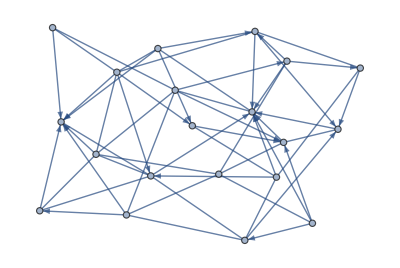

```mathematica
RandomMixedGraph[{20,54},.75]
```

Generate a graph with 0.5 directed edges:

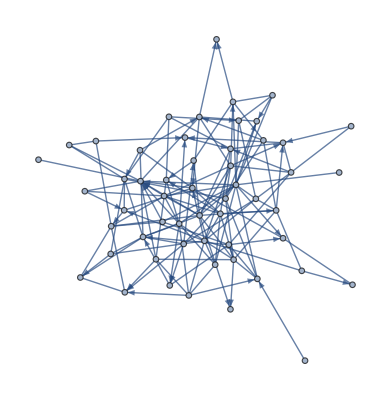

```mathematica
RandomMixedGraph[{54,148},0.5]
```

Where are the usage messages for the three-argument case, and the case where the first argument is a graph distribution? Please document them if you are going to show them in the examples.

Generate a list of random mixed graphs:

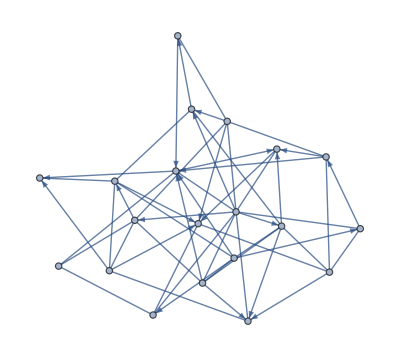
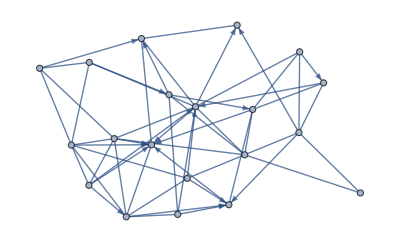
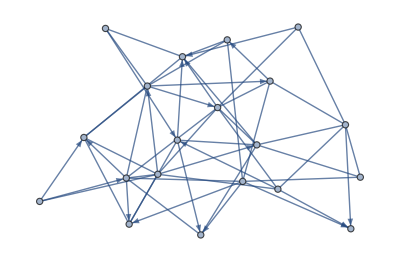

```mathematica
RandomMixedGraph[{20,54},0.68,3]
```

Generate an array of mixed graphs:

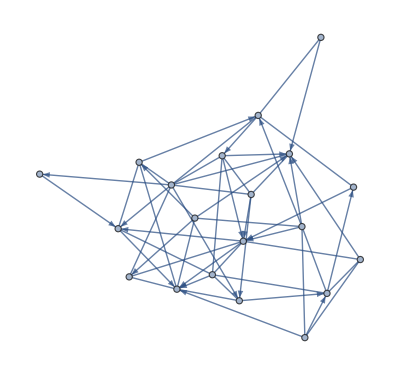
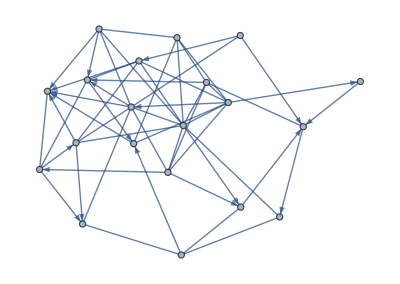
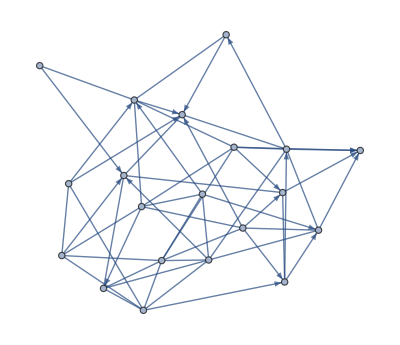
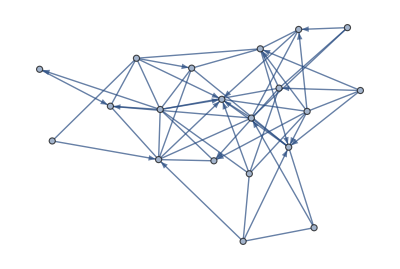
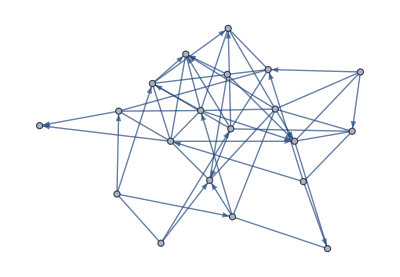
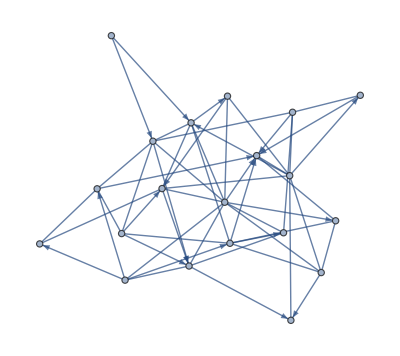

```mathematica
RandomMixedGraph[{20,54},0.68,{2,3}]
```

Generate a random spatial graph with 148 nodes and 0.68 directed edges:

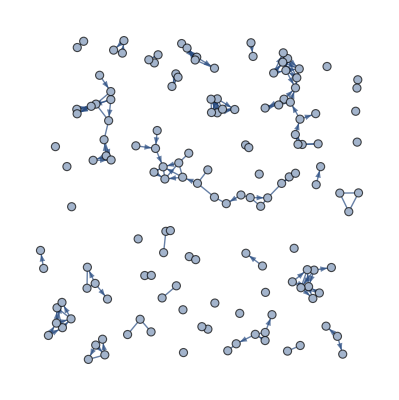

```mathematica
RandomMixedGraph[SpatialGraphDistribution[148,0.07],0.68]
```

Generate a list of random mixed graphs with the Barabasi-Albert graph distribution:

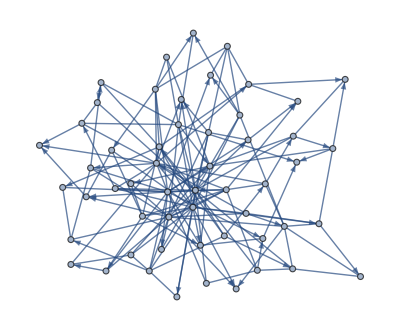
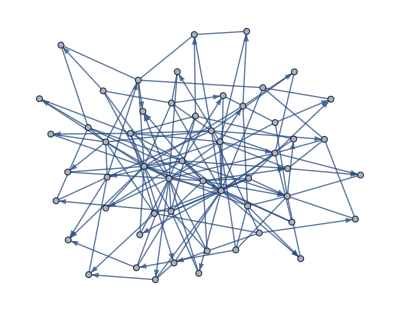
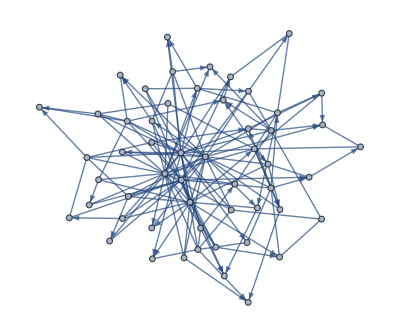
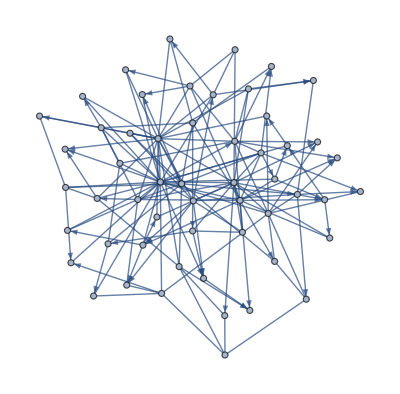
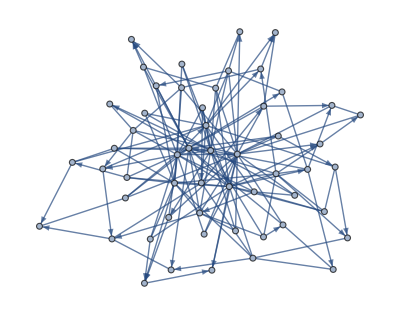
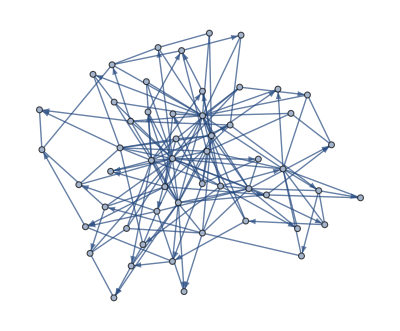
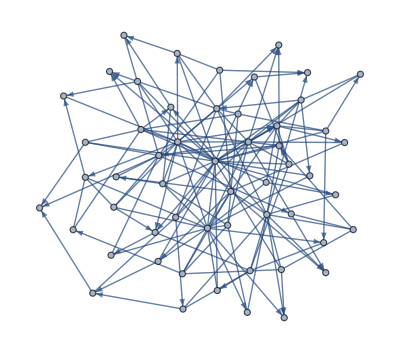

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,7]
```

Generate a 2x3 array of random graphs based on PriceGraphDistribution:

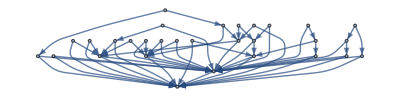
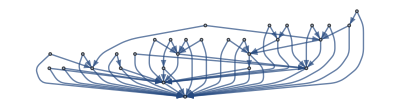
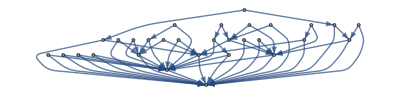
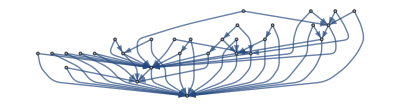
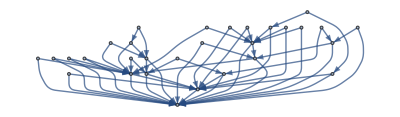
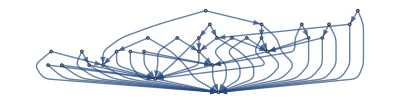
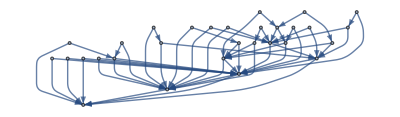

```mathematica
RandomMixedGraph[PriceGraphDistribution[30,2,1],0.68,7]
```

### Applications

Make a big mixed graph:

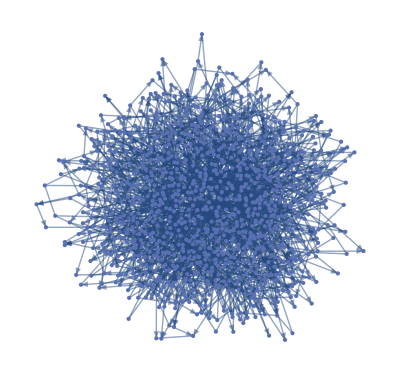

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[1096,2],0.68]
```

Evaluate if a mixed graph has a Hamiltonian cycle:

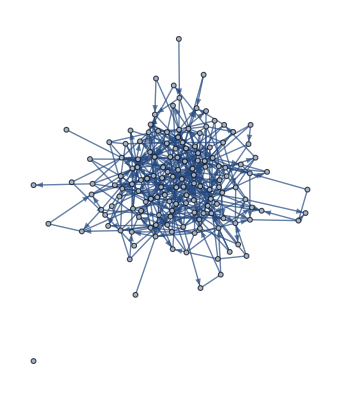

```mathematica
𝒢=RandomMixedGraph[{148,403},0.68]
```

```mathematica
HamiltonianGraphQ[𝒢]
```

False

Find the graph union of two mixed graphs:

```mathematica
GraphUnion@@Table[RandomMixedGraph[{20,54},0.68],3]
```

-Graphics-

Make an indexed mixed graph:

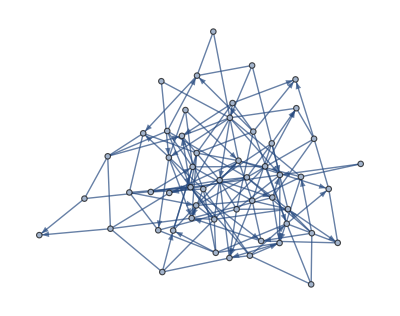

```mathematica
IndexGraph[RandomMixedGraph[{54,148},EulerGamma]]
```

Reverse a mixed graph's directed edges:

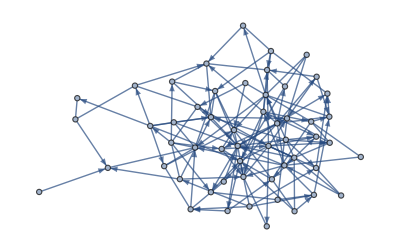

```mathematica
ReverseGraph[RandomMixedGraph[{54,148},EulerGamma]]
```

Compute the graph product for various definitions for two mixed graphs:

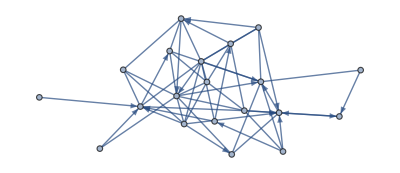

```mathematica
𝒢=RandomMixedGraph[{20,54},EulerGamma]
```

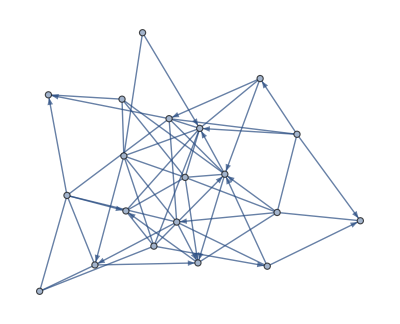

```mathematica
ℋ=RandomMixedGraph[{20,54},EulerGamma]
```

The graphs can be very very big:

```mathematica
Table[GraphProduct[𝒢,ℋ, op, 
  PlotLabel -> Style[op, 8]], {op, {"Cartesian", "Conormal", 
   "Lexicographical", "Normal", "Rooted", "Tensor"}}]
```

-Graphics-

Apply binary graph operations to two small mixed graphs:

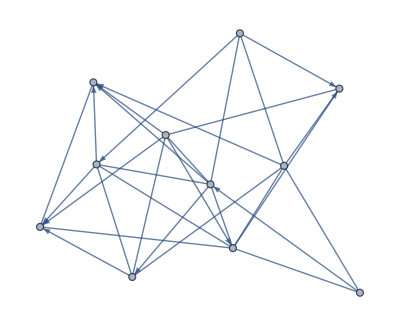

```mathematica
𝒢=RandomMixedGraph[{11,29},EulerGamma]
```

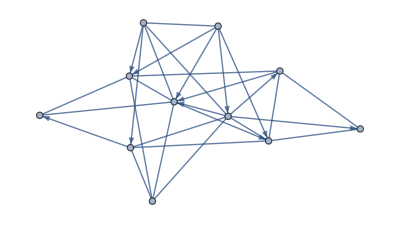

```mathematica
ℋ=RandomMixedGraph[{11,29},EulerGamma]
```

```mathematica
"Cartesian","Conormal","Lexicographical","Normal","Rooted","Tensor"
```

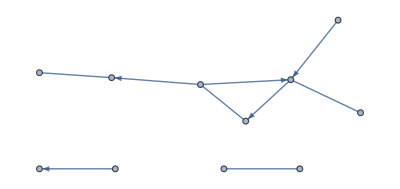
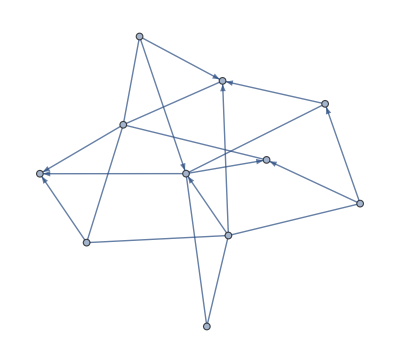
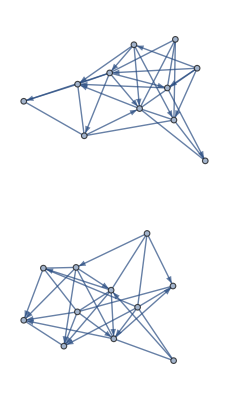
<|Boolean Graph Xor→-Graphics-,Boolean Graph Nand→-Graphics-,Graph Intersection→-Graphics-,Graph Union→-Graphics-,Graph Difference→-Graphics-,Graph Disjoint Union→-Graphics-,Cartesian Graph Product→-Graphics-,Conormal Graph Product→-Graphics-,Lexicographical Graph Product→-Graphics-,Normal Graph Product→-Graphics-,Rooted Graph Product→-Graphics-,Tensor Graph Product→-Graphics-,Graph Join→-Graphics-,Graph Sum→-Graphics-|>

```mathematica
AssociationThread[{"Boolean Graph Xor","Boolean Graph Nand","Graph Intersection","Graph Union","Graph Difference","Graph Disjoint Union","Cartesian Graph Product","Conormal Graph Product","Lexicographical Graph Product","Normal Graph Product","Rooted Graph Product","Tensor Graph Product","Graph Join","Graph Sum"},Map[(graphOperation↦graphOperation[𝒢,ℋ]),{BooleanGraph[Xor,##]&,BooleanGraph[Nand,##]&,GraphIntersection,GraphUnion,GraphDifference,GraphDisjointUnion,GraphProduct[##,"Cartesian"]&,GraphProduct[##,"Conormal"]&,GraphProduct[##,"Lexicographical"]&,GraphProduct[##,"Normal"]&,GraphProduct[##,"Rooted"]&,GraphProduct[##,"Tensor"]&,GraphJoin,GraphSum}]]
```

Compute unary graph operations on a large random mixed graph:

```mathematica
AssociationThread[{"Graph Power 2","Graph Complement"},Map[(graphOperation↦graphOperation[𝒢]),{GraphPower[##,2]&,GraphComplement}]]
```

<|Graph Power 2→-Graphics-,Graph Complement→-Graphics-|>

### Properties and Relations

Verify the output of the function produces a mixed graph:

```mathematica
MixedGraphQ[RandomMixedGraph[{148,403},.75]]
```

True

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

graph

directed graph

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

RandomGraph

SpatialGraphDistribution

### Related Resource Objects

OrientedGraphQ

TransitiveGraphQ

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

I changed the definition and updated the function. I copied the definition from the paclet Mixed Graphs.